```mathematica
Quit
```

```mathematica
n0=1; 
r0=1;el=1;b0=1;c=1;
```

```mathematica
n[r_]=n0*(1-(r/r0)^2)
```

1-r^2

```mathematica
Chi[x_,y_] = c/(4*Pi*n[Sqrt[x^2+y^2]]*el*y^2)
```

1/(4 π y^2 (1-x^2-y^2))

```mathematica
Chi0 =  c/(4*Pi*n0*el*r0^2);
```

```mathematica
BChi[x_,y_]=b0*r0*(Chi0/Chi[x,y])^2
```

y^4 (1-x^2-y^2)^2

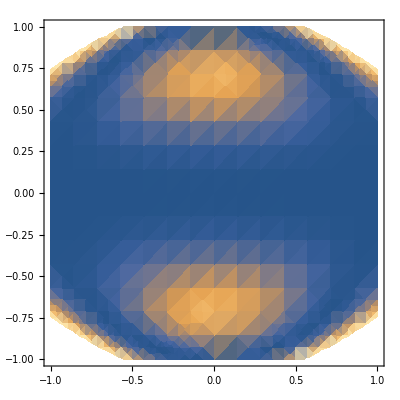

```mathematica
DensityPlot[BChi[x,y], {x,-r0,r0},{y,-r0,r0}]
```

```mathematica
BChiCyl[r_,theta_,z_]={0, BChi[z, r],b0}
```

{0,r^4 (1-r^2-z^2)^2,1}

```mathematica
dBdt=-Curl[Cross[c/(4*Pi*n[Sqrt[r^2+z^2]]*el)*Curl[BChiCyl[r,theta,z], {r,theta,z},"Cylindrical"],BChiCyl[r,theta,z]], {r,theta,z},"Cylindrical"]*HeavisideTheta[r0^2-r^2-z^2]
```

{-(r^4 HeavisideTheta[1-r^2-z^2])/π,((r^7 z)/(2 π)-(r^9 z)/π+(r^11 z)/(2 π)-(r^7 z^3)/π+(r^9 z^3)/π+(r^7 z^5)/(2 π)) HeavisideTheta[1-r^2-z^2],(5 r^3 z HeavisideTheta[1-r^2-z^2])/π}

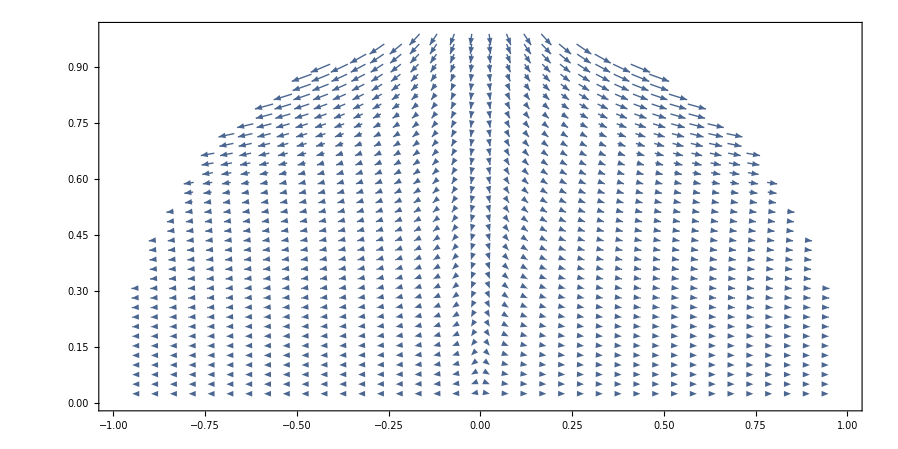

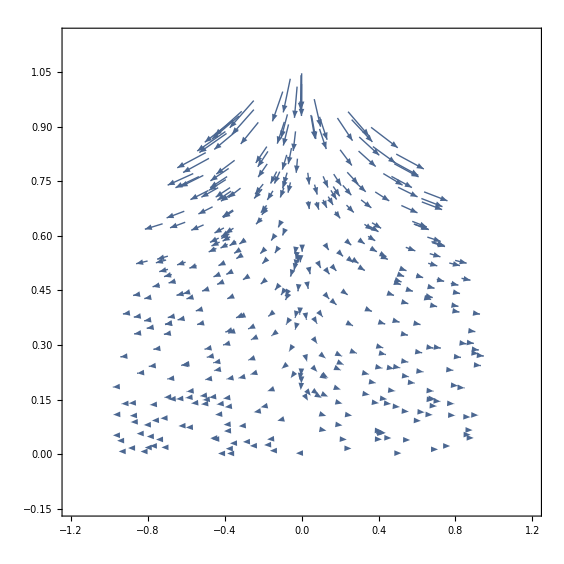

```mathematica
VectorPlot[{dBdt.{0,0,1},dBdt.{1,0,0}},{z,-r0,r0},{r,-0,r0},VectorPoints->{40,40},PlotRange->{{-1,1},{0,1}},AspectRatio->1/2]
```

```mathematica
BChiCyl[r,theta,z]
```

{0,r^4 (1-r^2-z^2)^2,1}

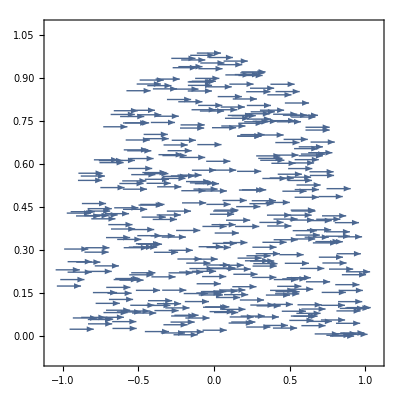

```mathematica
VectorPlot[{BChiCyl[r,theta,z].{0,0,1},BChiCyl[r,theta,z].{1,0,0}}*HeavisideTheta[r0^2-r^2-z^2],{z,-r0,r0},{r,-0,r0},VectorPoints->RandomReal[{-r0,r0},{1000,2}]]
```